## Bayesian Statistics, Problem Set 11 (Nov. 5) SOLUTION

## The Mug Breakage Problem

### Step 1 — Computing the Likelihood Function

Act as if a were known. (Remember the likelihood is P(data|a). That means we are pretending that a is given.

(a) Write down the probability of having 1 mug broken in the first week. You may have to remind yourself the formula for the Poisson distribution. It was on p. 59 of Young. You are just being asked to plug n=1 into this formula.

a^1/(1!)e^-a=a e^-a

(b) Repeat, but with n=6 for the second week.

a^6/(6!)e^-a=a^6/720 e^-a

(c) Repeat, but with n=4 for the third week.

a^4/(4!)e^-a=a^4/24 e^-a

(d) Take the product of what you got in (a), (b), and (c). This is the likelihood of getting this data.

a e^-a x a^6/720 e^-axa^4/24 e^-a=a^11/(720·24)e^(-3a)

What a crazy function!

### Step 2 — Tabulate the Likelihood

```mathematica
poisson[n_, a_]:=a^n/Factorial[n] Exp[-a];likelihood[{n1_, n2_, n3_}, a_]:=poisson[n1, a]*poisson[n2, a]*poisson[n3, a];
TableForm[Table[{a,likelihood[{1, 6, 4}, a]}, {a, 0, 8, 0.5}], TableHeadings->{None, {"a", "P(data|a)"}}]
```

a | P(data|a)
0. | 0.
0.5 | 6.30499×10^-9
1. | 2.8812×10^-6
1.5 | 0.0000556077
2. | 0.000293778
2.5 | 0.000763111
3. | 0.00126514
3.5 | 0.00153855
4. | 0.00149136
4.5 | 0.00121568
5. | 0.000864389
5.5 | 0.000550284
6. | 0.000319756
6.5 | 0.000172092
7. | 0.0000867662
7.5 | 0.0000413527
8. | 0.0000187663

### Step 3 — Graph the Likelihood

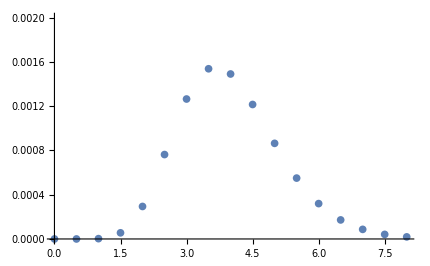

```mathematica
ListPlot[Table[{a, likelihood[{1, 6, 4}, a]}, {a, 0, 8, 0.5}], PlotRange->{{0, 8},{0,0.002}}]
```

### Step 4 — Tabulate the Product of the Likelihood and the Prior

In Step 2, you tabulated the likelihood. Take a look at the graph of the prior. It is 0 unless a is between 2 and 6. If a is between 2 and 6, it is 1/4. Using these facts, you should be able to quickly tabulate the product of the likelihood and the prior.

```mathematica
prior[a_]:=If[2<=a<=6, 0.25, 0];
product[a_]:=likelihood[{1, 6, 4}, a]*prior[a];
TableForm[Table[{a,product[a]}, {a, 0, 8, 0.5}], TableHeadings->{None, {"a", "P(data|a)*P(a)"}}]
```

a | P(data|a)*P(a)
0. | 0.
0.5 | 0.
1. | 0.
1.5 | 0.
2. | 0.0000734445
2.5 | 0.000190778
3. | 0.000316286
3.5 | 0.000384638
4. | 0.00037284
4.5 | 0.000303919
5. | 0.000216097
5.5 | 0.000137571
6. | 0.0000799391
6.5 | 0.
7. | 0.
7.5 | 0.
8. | 0.

### Step 5 — Graph the Product of the Likelihood and the Prior

In Step 4, you tabulated the product of the likelihood and the prior. Now you are going to graph it.

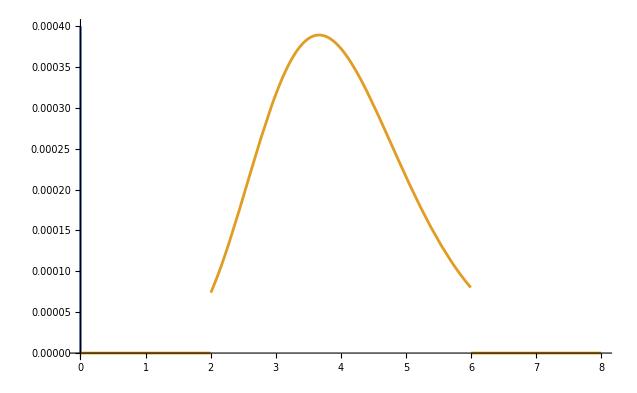

```mathematica
Plot[{a, product[a]},{a,0,8}, PlotRange->{{0, 8},{0,0.0004}}]
```

### Remaining Steps

There are still two a few more steps to go!! Remember that we are trying to compute

P(a^*|data)Δ a^*=(P(data|a^*)P(a^*)Δ a^*)/(∫_a_min^a_max P(data|a)P(a)da)

Step 6 is to do the integral in the denominator, 
Step 7 is to make a table of the posterior, which is P(data|a^*)P(a^*) divided by the denominator from Step 6.
Step 8 is to plot the posterior.
Step 9 is to interpret the posterior.

HOWEVER! We have to leave something for our presenters to do, so we will stop at Step 5.